{{0},{0},{0},{0},{1},{0},{-1},{-1},{1},{3},{-1},{-6},{-2},{9},{7},{-12},{-15},{11},{27},{-5},{-40},{-10},{52},{33},{-58},{-67},{52},{109},{-28},{-152},{-20},{188},{95},{-205},{-194},{188},{311},{-123},{-430},{-2},{530},{190},{-584},{-440},{559},{737},{-424},{-1052},{148},{1346},{295},{-1565},{-926},{1639},{1772},{-1476},{-2883},{925},{4410},{364},{-6934},{-3778},{14363},{32767},{32767},{14363},{-3778},{-6934},{364},{4410},{925},{-2883},{-1476},{1772},{1639},{-926},{-1565},{295},{1346},{148},{-1052},{-424},{737},{559},{-440},{-584},{190},{530},{-2},{-430},{-123},{311},{188},{-194},{-205},{95},{188},{-20},{-152},{-28},{109},{52},{-67},{-58},{33},{52},{-10},{-40},{-5},{27},{11},{-15},{-12},{7},{9},{-2},{-6},{-1},{3},{1},{-1},{-1},{0},{1},{0},{0},{0},{0},{}}

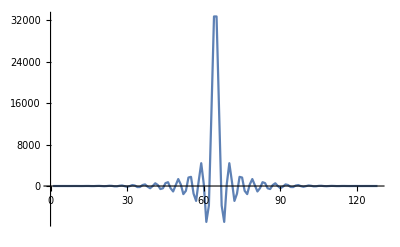

```mathematica
taps = Import["/home/john/Code/mathematica/dsp/taps.dat"];
taps16 = Round[(2^15-1)/(Max@taps)*taps]
ListLinePlot[Flatten@taps16,PlotRange->All]
```

```mathematica
fmax := 600;
di:=1/(4*fmax);
window = 1/(2*di);
```

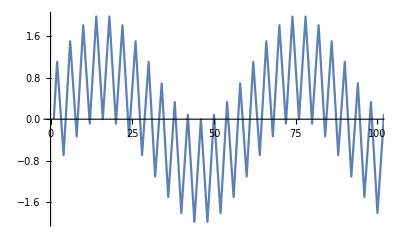

```mathematica
data = Table[Sin[40*2*Pi*x]+Sin[600*2*Pi*x],{x,0,2Pi,di}];
ListLinePlot[data,PlotRange->{{0,100},All}]
```

```mathematica
NonZero[n_]:=If[n==0,1,n];
min = Min[Abs[NonZero/@data]];
corrected = Round@(data/min);
```

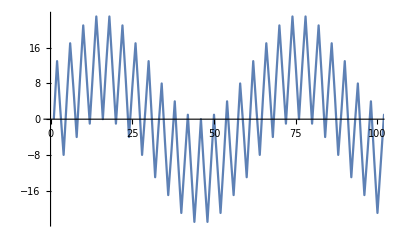

```mathematica
ListLinePlot[corrected,PlotRange->{{0,100},All}]
```

```mathematica
Export["/home/john/Code/mathematica/dsp/test_input.dat",corrected]
```

/home/john/Code/mathematica/dsp/test_input.dat

```mathematica
Export["/home/john/Code/mathematica/dsp/test_taps_ints.mem",taps16,"Integer16"]
```

/home/john/Code/mathematica/dsp/test_taps_ints.mem